Kruskal’s Algorithms

```mathematica
edges={a<->b,a<->c,a <-> d,b <-> d,c <-> d,c <-> f, e <-> f, d <-> f,b <->c}
weights={4,1,3,4,2,4,5,6,4}
edgeweightrule=Thread[#1-> #2 &[edges,weights]]
```

{a<->b,a<->c,a<->d,b<->d,c<->d,c<->f,e<->f,d<->f,b<->c}

{4,1,3,4,2,4,5,6,4}

{a<->b→4,a<->c→1,a<->d→3,b<->d→4,c<->d→2,c<->f→4,e<->f→5,d<->f→6,b<->c→4}

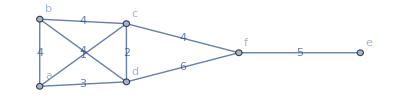

```mathematica
Graph[edges,EdgeWeight->weights, VertexLabels -> "Name",EdgeLabels->edgeweightrule]
```

```mathematica
lighterEdge[e1_,e2_]:=If[Last[e1]<=Last[e2],e1,e2]
Fold[lighterEdge,edgeweightrule]
```

a<->c→1

```mathematica
For[lightestEdge=0;i=0;ed=edgeweightrule;MST={},Length[ed]>0,
lightestEdge=Fold[lighterEdge,ed];
MST=If[AcyclicGraphQ[Graph[Map[First[#1]&,Append[MST,lightestEdge]]]],Append[MST,lightestEdge],MST];
ed=DeleteCases[ed,edge_/;First[edge]==First[lightestEdge]];
i++
]
```

```mathematica
Map[Last[#]&,MST]
```

{1,2,4,4,5}

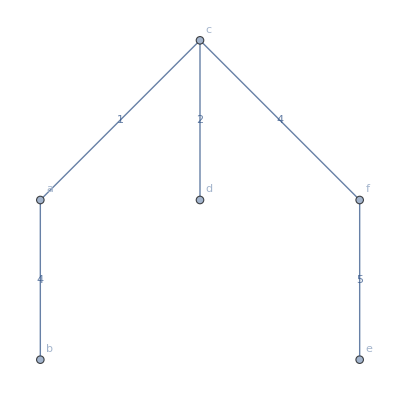

```mathematica
Graph[Map[First[#]&,MST],VertexLabels->"Name",EdgeLabels->MST]
```